```mathematica
SetDirectory[NotebookDirectory[]]
```

H:\Data\Documents\02_FPP\03_classes\1.stopnja\IPFM_01\lectures\grm\02_funkcije_kompleksna\figs

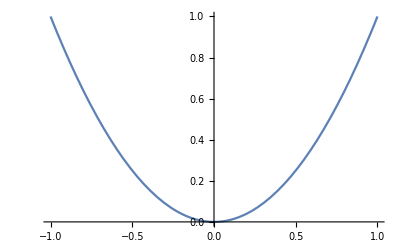

```mathematica
pl=Plot[x^2,{x,-1,1}]
```

```mathematica
Export["fig_01_03.pdf",pl]
```

fig_01_03.pdf

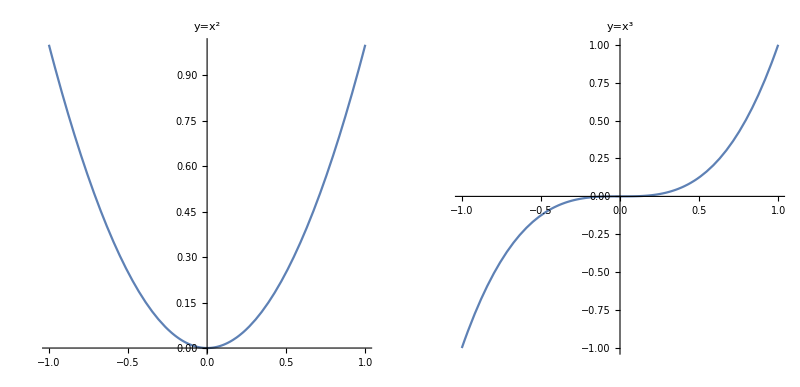

```mathematica
pl=GraphicsGrid[{{Plot[x^2,{x,-1,1},AspectRatio->1,PlotLabel->"y=x^2"],Plot[x^3,{x,-1,1},AspectRatio->1,PlotLabel->"y=x^3"]}}]
```

```mathematica
Export["fig_01_04.pdf",pl]
```

fig_01_04.pdf

## Metoda najmanjših kvadratov

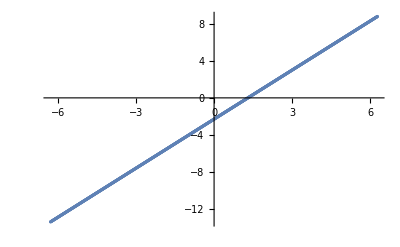

```mathematica
k=1.77;
n=-2.3;

f[x_]:=k x+n;
xyD=Table[{x,f[x]},{x,-2 π,2 π,0.01}];

ListPlot[xyD]
```

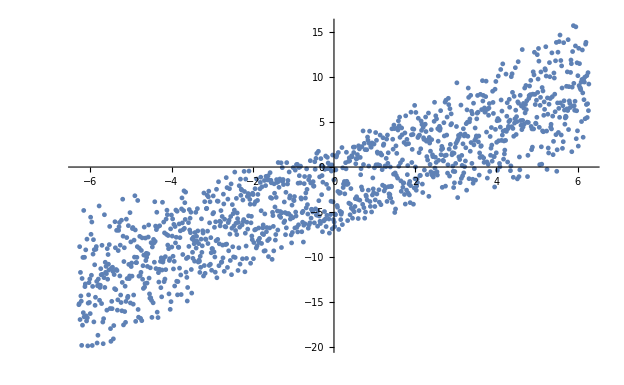

fig_02_01.pdf

```mathematica
xyR=Table[{x,k RandomReal[{0.6,1.4}] x+n RandomReal[{0.6,1.4}]+4 Sin[RandomReal[{0,2π}]]},{x,-2 π,2 π,0.01}];

plRPts=ListPlot[xyR]
Export["fig_02_01.pdf",plRPts]
```

```mathematica
line= Fit[xyR, {1,x},x]
pl=Plot[line,{x,-2 π,2 π},PlotStyle->Red];
Export["fig_02_02.pdf",Show[plRPts,pl]]
```

-2.31376+1.75671 x

fig_02_02.pdf

## Funkcije

### Potenčna

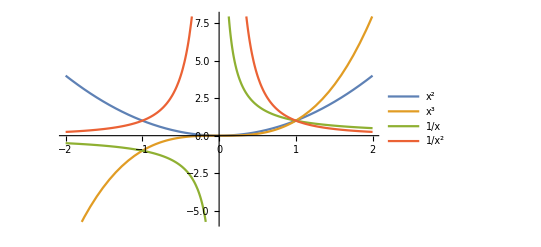

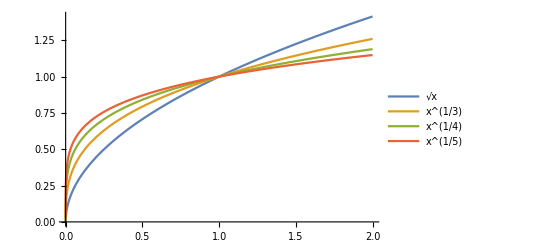

fig_02_04.pdf

fig_02_05.pdf

```mathematica
pl1=Plot[{x^2,x^3,x^-1,x^-2},{x,-2,2},PlotLegends->"Expressions"]
pl2=Plot[{x^(1/2),x^(1/3),x^(1/4),x^(1/5)},{x,0,2},PlotLegends->"Expressions"]
Export["fig_02_04.pdf",pl1]
Export["fig_02_05.pdf",pl2]
```

### Lagrange Polynomial

4.13×10^-7 (-1.56×10^9+4.23×10^9 x-1.03×10^9 x^2-3.15×10^8 x^3+1.46×10^8 x^4-1.67×10^7 x^5+582000. x^6)

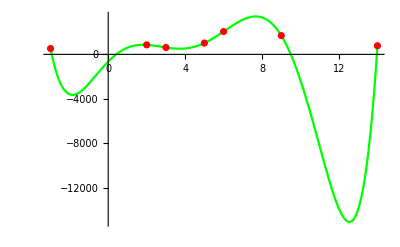

fig_02_06.pdf

```mathematica
data={{-3,523},{2,856},{3,617},{5,1017},{6,2054},{9,1689},{14,777}};
lip=InterpolatingPolynomial[data,x]//Expand//Simplify;
N[lip,3]
pl=Show[Plot[lip,{x,-3,14},PlotStyle->Green],ListPlot[data,PlotStyle->Red]]
Export["fig_02_06.pdf",pl]
```

### Logaritem

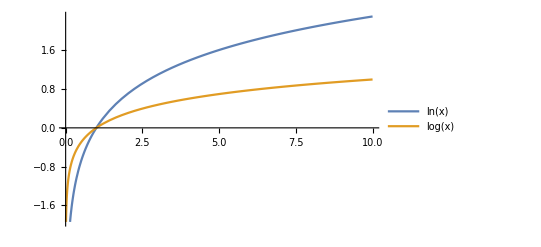

fig_02_07.pdf

```mathematica
pl=Plot[{Log[x],Log10[x]},{x,0,10},PlotLegends->{"ln(x)","log(x)"}]
Export["fig_02_07.pdf",pl]
```

### Kotne funcije

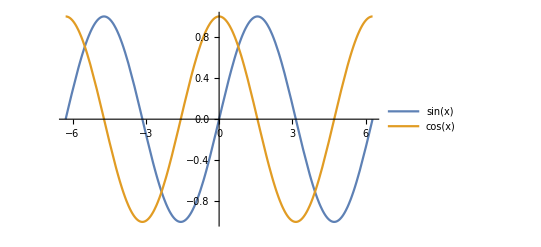

fig_02_08.pdf

```mathematica
pl=Plot[{Sin[x],Cos[x]},{x,-2π,2π},PlotLegends->"Expressions"]
Export["fig_02_08.pdf",pl]
```

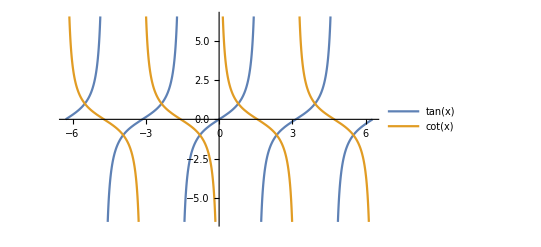

fig_02_09.pdf

```mathematica
pl=Plot[{Tan[x],Cot[x]},{x,-2π,2π},PlotLegends->"Expressions"]
Export["fig_02_09.pdf",pl]
```

### Hiperbolične

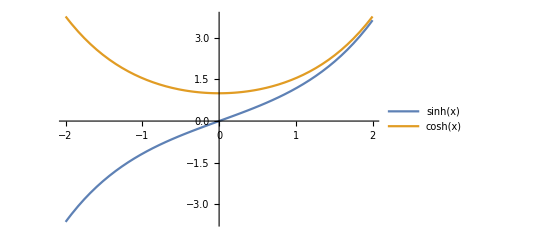

fig_02_10.pdf

```mathematica
pl=Plot[{Sinh[x],Cosh[x]},{x,-2,2},PlotLegends->"Expressions"]
Export["fig_02_10.pdf",pl]
```